# (4) Neural activity

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
dir ="../cSrc/";
(*dir = "../AnalysisData/best_offset/";*)
```

## Dimension Reduction

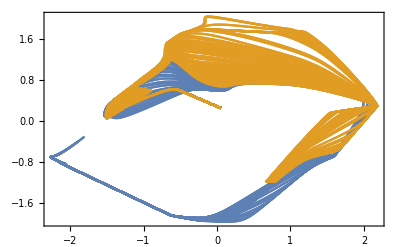

```mathematica
d1 = Flatten[{ba1,bc1}];
d2 = Flatten[{ba2,bc2}];
d3 = Flatten[{ba3,bc3}];
vectors =Transpose[{d1,d2,d3}];
dr=DimensionReduction[vectors,2];
Show[{ListLinePlot[Table[dr[Transpose[{ba1[[x]],ba2[[x]],ba3[[x]]}]],{x,1,100}],PlotStyle->cd[[1]]],
ListLinePlot[Table[dr[Transpose[{bc1[[x]],bc2[[x]],bc3[[x]]}]],{x,1,100}],PlotStyle->cd[[2]]]},PlotRange->All,Frame->True]
```

Transpose::nmtx: The first two levels of {«1»,«2»,{1,0.999999,0.999998,0.999994,0.999984,0.99996,0.999904,0.999787,0.999547,0.999086,0.998235,0.996737,0.994204,0.990089,0.983652,0.973944,0.959804,0.9399,0.912796,0.877075,0.831517,0.775342,0.708521,«5»,0.230695,0.17477,0.130842,0.0974901,0.0727319,0.0545812,0.0413352,0.0316564,0.0245466,0.0192826,0.0153477,0.0123755,0.0101061,0.00835427,0.00698743,0.00590976,0.00505152,0.00436143,0.00380147,0.00334316,0.00296498,0.00265052,«69950»}} cannot be transposed.

DimensionReducerFunction::mlbddataev: The data being evaluated is not formatted correctly.

Part::partw: Part 2 of {{1,0.999999,0.999998,0.999994,0.999984,0.99996,0.999904,0.999787,0.999547,0.999086,0.998235,0.996737,0.994204,0.990089,0.983652,0.973944,0.959804,0.9399,0.912796,0.877075,0.831517,0.775342,0.708521,«5»,0.230695,0.17477,0.130842,0.0974901,0.0727319,0.0545812,0.0413352,0.0316564,0.0245466,0.0192826,0.0153477,0.0123755,0.0101061,0.00835427,0.00698743,0.00590976,0.00505152,0.00436143,0.00380147,0.00334316,0.00296498,0.00265052,«69950»}} does not exist.

Transpose::nmtx: The first two levels of {«1»,{«1»},«1»,{{1,0.999999,0.999998,0.999994,0.999984,0.99996,0.999904,0.999787,0.999547,0.999086,0.998235,0.996737,0.994204,0.990089,0.983652,0.973944,0.959804,0.9399,0.912796,0.877075,0.831517,0.775342,0.708521,«6»,0.17477,0.130842,0.0974901,0.0727319,0.0545812,0.0413352,0.0316564,0.0245466,0.0192826,0.0153477,0.0123755,0.0101061,0.00835427,0.00698743,0.00590976,0.00505152,0.00436143,0.00380147,0.00334316,0.00296498,0.00265052,«69950»}}⟦2⟧} cannot be transposed.

DimensionReducerFunction::mlbddataev: The data being evaluated is not formatted correctly.

Part::partw: Part 3 of {{1,0.999999,0.999998,0.999994,0.999984,0.99996,0.999904,0.999787,0.999547,0.999086,0.998235,0.996737,0.994204,0.990089,0.983652,0.973944,0.959804,0.9399,0.912796,0.877075,0.831517,0.775342,0.708521,«5»,0.230695,0.17477,0.130842,0.0974901,0.0727319,0.0545812,0.0413352,0.0316564,0.0245466,0.0192826,0.0153477,0.0123755,0.0101061,0.00835427,0.00698743,0.00590976,0.00505152,0.00436143,0.00380147,0.00334316,0.00296498,0.00265052,«69950»}} does not exist.

Transpose::nmtx: The first two levels of {«1»,{«1»},«1»,{{1,0.999999,0.999998,0.999994,0.999984,0.99996,0.999904,0.999787,0.999547,0.999086,0.998235,0.996737,0.994204,0.990089,0.983652,0.973944,0.959804,0.9399,0.912796,0.877075,0.831517,0.775342,0.708521,«6»,0.17477,0.130842,0.0974901,0.0727319,0.0545812,0.0413352,0.0316564,0.0245466,0.0192826,0.0153477,0.0123755,0.0101061,0.00835427,0.00698743,0.00590976,0.00505152,0.00436143,0.00380147,0.00334316,0.00296498,0.00265052,«69950»}}⟦3⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

DimensionReducerFunction::mlbddataev: The data being evaluated is not formatted correctly.

General::stop: Further output of DimensionReducerFunction::mlbddataev will be suppressed during this calculation.

Part::partw: Part 4 of {{1,0.999999,0.999998,0.999994,0.999984,0.99996,0.999904,0.999787,0.999547,0.999086,0.998235,0.996737,0.994204,0.990089,0.983652,0.973944,0.959804,0.9399,0.912796,0.877075,0.831517,0.775342,0.708521,«5»,0.230695,0.17477,0.130842,0.0974901,0.0727319,0.0545812,0.0413352,0.0316564,0.0245466,0.0192826,0.0153477,0.0123755,0.0101061,0.00835427,0.00698743,0.00590976,0.00505152,0.00436143,0.00380147,0.00334316,0.00296498,0.00265052,«69950»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

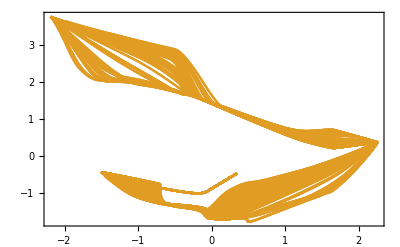

```mathematica
d1 = Flatten[{ba1,bc1}];
d2 = Flatten[{ba2,bc2}];
d3 = Flatten[{ba3,bc3}];
d4 = Flatten[{ba4,bc4}];
d5 = Flatten[{ba5,bc5}];
d6 = Flatten[{ba6,bc6}];
d7 = Flatten[{ba7,bc7}];
vectors =Transpose[{d1,d2,d3,d4}];
dr=DimensionReduction[vectors,2];
Show[{ListLinePlot[Table[dr[Transpose[{ba1[[x]],ba2[[x]],ba3[[x]],ba4[[x]]}]],{x,1,100}],PlotStyle->cd[[1]]],
ListLinePlot[Table[dr[Transpose[{bc1[[x]],bc2[[x]],bc3[[x]],bc4[[x]]}]],{x,1,100}],PlotStyle->cd[[2]]]},PlotRange->All,Frame->True]
```

## Random NN

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
a=Import["nn.dat"];
```

Import::nffil: File nn.dat not found during Import.

```mathematica
b = Transpose[Take[a,{2000,25000,100},{1,100}]];
```

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{2000,25000,100},{1,100}].

```mathematica
ListLinePlot[b,Frame->False,Axes->False,FrameTicks->False,AspectRatio->1/8,ImageSize->1000]
Export["randomneuralactivity.eps",%]
```

ListLinePlot::lpn: Transpose[Take[$Failed,{2000,25000,100},{1,100}]] is not a list of numbers or pairs of numbers.

ListLinePlot[Transpose[Take[$Failed,{2000,25000,100},{1,100}]],Frame→False,Axes→False,FrameTicks→False,AspectRatio→1/8,ImageSize→1000]

randomneuralactivity.eps

## Task 1: Object Categorization

```mathematica
ba1=Import[StringJoin[dir,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir,"B_avoid_n5.dat"]];
ba6=Import[StringJoin[dir,"B_avoid_n6.dat"]];
ba7=Import[StringJoin[dir,"B_avoid_n7.dat"]];
bc1=Import[StringJoin[dir,"B_approach_n1.dat"]];
bc2=Import[StringJoin[dir,"B_approach_n2.dat"]];
bc3=Import[StringJoin[dir,"B_approach_n3.dat"]];
bc4=Import[StringJoin[dir,"B_approach_n4.dat"]];
bc5=Import[StringJoin[dir,"B_approach_n5.dat"]];
bc6=Import[StringJoin[dir,"B_approach_n6.dat"]];
bc7=Import[StringJoin[dir,"B_approach_n7.dat"]];
```

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[bc1,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba1,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc2,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba2,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc3,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba3,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc4,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba4,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc5,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba5,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc6,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba6,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc7,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba7,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
(*Export["ObjectRecog.eps",%]*)
```

-Graphics-

## Task 2: Perceiving affordances

```mathematica
aa1=Import[StringJoin[dir,"A_avoid_n1.dat"]];
aa2=Import[StringJoin[dir,"A_avoid_n2.dat"]];
aa3=Import[StringJoin[dir,"A_avoid_n3.dat"]];
aa4=Import[StringJoin[dir,"A_avoid_n4.dat"]];
aa5=Import[StringJoin[dir,"A_avoid_n5.dat"]];
aa6=Import[StringJoin[dir,"A_avoid_n6.dat"]];
aa7=Import[StringJoin[dir,"A_avoid_n7.dat"]];
ac1=Import[StringJoin[dir,"A_approach_n1.dat"]];
ac2=Import[StringJoin[dir,"A_approach_n2.dat"]];
ac3=Import[StringJoin[dir,"A_approach_n3.dat"]];
ac4=Import[StringJoin[dir,"A_approach_n4.dat"]];
ac5=Import[StringJoin[dir,"A_approach_n5.dat"]];
ac6=Import[StringJoin[dir,"A_approach_n6.dat"]];
ac7=Import[StringJoin[dir,"A_approach_n7.dat"]];
```

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[ac1,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa1,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac2,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa2,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac3,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa3,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac4,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa4,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac5,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa5,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac6,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa6,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac7,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa7,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
(*Export["PercAff.eps",%]*)
```

-Graphics-